```mathematica
E^11.
```

59874.1

```mathematica
E^(-30.)*10^6
```

9.35762×10^-8

```mathematica
10^6
```

1000000

```mathematica
B0
```

0.047

```mathematica
(E^(-.78/(8.62*10^(-5)*310.928)))
```

2.29629×10^-13

```mathematica
individden[x_]:=E^(-19.63)*x^(-.78)/(E^(-.78/(8.62*10^(-5)*313.15)))/1000^2(*N m^-2*)
```

```mathematica
individden[x]
```

0.0105704/x^0.78

```mathematica
individden[10^(-2.)]
%*10^(-2)
```

0.383788

0.00383788

```mathematica
individden[x]
```

0.0105704/x^0.78

```mathematica
80/1000^2.
```

0.00008

```mathematica
individden[10^(-3.)]
individden[10^(6.)]
```

2.31255

2.20847×10^-7

```mathematica
E^(-10.)*1000
```

0.0453999

```mathematica
(*dF/dt terms*)
Ftmp=individden[M]*M;
Htmp=Ftmp;
(Log[2]/τLam)*Ftmp
(1/τRho)*Htmp
-(1/τSig)*(1)*Ftmp
Total[{%,%%,%%%}]
```

(M individden[M] Log[2])/τLam

(M individden[M])/τRho

-(M individden[M])/τSig

(M individden[M])/τRho-(M individden[M])/τSig+(M individden[M] Log[2])/τLam

```mathematica
(*dH/dt terms*)
(1/τSig)*(1)*Ftmp
-(1/τRho)*Htmp
-( 1/τMu)*Htmp
Total[{%,%%,%%%}]
```

1.43446×10^-7

-5.98919×10^-9

-6.19158×10^-8

7.5541×10^-8

```mathematica
BLam
BRho
Ed
```

3.62079×10^13

2.59574×10^13

18200

```mathematica
M
```

1000000

```mathematica
YF
```

5.02653×10^-10

```mathematica
(1/τRho)
YH
```

2.71192×10^-8

7.0115×10^-10

```mathematica
(1/τRho)/YH
PH
(Log[2]/τLam)/YF
PF
```

0.0000386782

8.16632×10^-8

0.0000203479

8.16632×10^-8

```mathematica
(*R terms*)
Rtmp=9162.57(*g/m^2*);
alpha*Rtmp
-((1/τRho)/YH+PH)*Htmp
-((Log[2]/τLam)/YF+PF)*Ftmp
Total[{%,%%,%%%}]
```

0.0000192414

-4.78059×10^-7

-2.45186×10^-7

0.0000185182

```mathematica
(-.78*10-19.63)
E^%
```

-27.43

1.22265×10^-12

```mathematica
Ratesfunc[x_] :=(
ts=x[[1]];
M=x[[2]];
B0=x[[3]];
Em=x[[4]];
Emprime=x[[5]];
η=x[[6]];
λ0=x[[7]];
γ=x[[8]];
ζ=x[[9]];
f0=x[[10]];
mm0=x[[11]];
alpha=x[[12]];
Ed=x[[13]];
c=x[[14]];
k=x[[15]];
χ=x[[16]];

(*TimeScales*)
a = B0/Em;
aprime =  B0/Emprime;
ϵLam = 0.95;
m0 = 0.00001;
ϵSig = (1-f0*M^γ/M);
ϵMu = (1-(f0*M^γ+mm0*M^ζ)/M);
τLam = -Log[(1-ϵLam^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
τRhoStart = -Log[(1-(ϵSig*ϵLam)^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
τRho = -Log[(1-ϵLam^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*M^(1/4))/aprime;
τRhoInvade = -Log[(1-(ϵLam*(1+χ))^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*M^(1/4))/aprime;
τSig = -M^(1/4)/aprime*Log[ϵSig];
τSigInvade =  -M^(1/4)/aprime*Log[ϵSig/(1+χ)];
τMu = -M^(1/4)/aprime*Log[ϵMu] -τSig;

(*Rates*)

ConsumerGrowth = ts*(Log[2]/τLam); (*Fecundity = 2*)

Starvation = ts*(1/τSig);
InvaderStarvation = ts*(1/τSigInvade);

Mortality=ts*( 1/τMu);

Recovery = ts*c/k*(1/τRho);
InvaderRecovery= ts*c/k*(1/τRhoInvade);
BLam=1/(3 a)ⅇ^(-(a τLam)/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam)/M^(1/4))) m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4))+ⅇ^((a τLam)/M^(1/4)) (-25+12 (m0/M)^(1/4)+6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam);
BRho=1/(3 a)M^(1/4) (ⅇ^(-(a τLam)/M^(1/4)) (-3 m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam)+ⅇ^(-(a τRhoStart)/M^(1/4)) (3 m0+M (48 ⅇ^((3 a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))+36 ⅇ^((a τRhoStart)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2+16 ⅇ^((a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (1-4 (m0/M)^(1/4)+6 √(m0/M)-4 (m0/M)^(3/4)))-3 a ⅇ^((a τRhoStart)/M^(1/4)) M^(3/4) τRhoStart));

YF=M*Ed/BLam;
YH=M*Ed/BRho;
PF=(B0*M^η)/M/Ed;
PH=PF;

StarveMaintenance = ts*PH*(YH/(c/k));
FullMaintenance = ts*((ConsumerGrowth/YF+PF)*(YH/(c/k)));
InvaderMaintenance = ts*((ConsumerGrowth/YF+(B0*(M*(1+χ))^η))*(YH/(c/k)));

ResourceGrowth = ts*alpha;

(*to check the dimensional form*)
βtmp=(ConsumerGrowth/YF+PF);


{ConsumerGrowth,Starvation,Mortality,Recovery,StarveMaintenance,FullMaintenance,ResourceGrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance,βtmp}
);
```

```mathematica
Clear[τRhoStart]
```

```mathematica
Integrate[((1-(1-(m0/M)^(1/4))*E^(-a*t/(4*M^(1/4)))))^4*M,{t,0,τLam}]
```

1/(3 a)ⅇ^(-(a τLam)/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam)/M^(1/4))) m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4))+ⅇ^((a τLam)/M^(1/4)) (-25+12 (m0/M)^(1/4)+6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam)

```mathematica
Integrate[((1-(1-(m0/M)^(1/4))*E^(-a*t/(4*M^(1/4)))))^4*M,{t,τRhoStart,τLam}]
```

1/(3 a)M^(1/4) (ⅇ^(-(a τLam)/M^(1/4)) (-3 m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam)+ⅇ^(-(a τRhoStart)/M^(1/4)) (3 m0+M (48 ⅇ^((3 a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))+36 ⅇ^((a τRhoStart)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2+16 ⅇ^((a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (1-4 (m0/M)^(1/4)+6 √(m0/M)-4 (m0/M)^(3/4)))-3 a ⅇ^((a τRhoStart)/M^(1/4)) M^(3/4) τRhoStart))

```mathematica
YH
```

1.42623×10^9

```mathematica
B0*M^η
```

1486.27

```mathematica
ResourceGrowth
```

2.1×10^-9

```mathematica
FullMaintenance-StarveMaintenance
```

-0.000488281

```mathematica
StarveMaintenance
```

4.23952×10^12

```mathematica
9071/2.
```

4535.5

```mathematica
parameters={
(*ts*)1,
(*M*)Mass =1,
(*B0*)4.7*10^(-2),
(*Em*)5774(*J/gram*),
(*Emprime*)7000 (*10000*),
(*η*)3/4,
(*λ0*)3.39*10^(-7),
(*γ*)1.19,
(*ζ*)1.00,
(*f0*)0.0202,
(*mm0*)0.383,
(*α*)2.10*10^(-9),
(*Ed*)18200,
(*c*)10,
(*k*)5,
(*χ*)chi};
RF =Ratesfunc[parameters]
(*GrowthOverM=RF[[1]];
StarvationOverM=RF[[2]];
MortalityOverM = RF[[3]];
RecoveryOverM=RF[[4]];
MaintenanceOverM = RF[[5]];
ResourcegrowthOverM=RF[[6]];*)
```

{3.27651×10^-7,0.000329022,0.0000135432,0.0000101001,1.5291×10^-7,1.37345×10^-6,2.1×10^-9,-(6.71429×10^-6)/Log[0.9798/(1+chi)],-(3.35714×10^-6)/Log[56.2894 (1-0.987259 (1+chi)^(1/4))],0.0592119 (0.0000206131+0.047 (1+chi)^(3/4)),0.0000231955}

```mathematica
individden[10^(6.)]
```

2.20847×10^-7

```mathematica
individden[10^(6.)]*10^(6.)(*g organism m^-2*)
βtmp*%(*βF; g grass g organism^-1 s^-1*)
biomassdentmp=9071.85(*g m^-2*)
alpha*biomassdentmp*.1
```

0.220847

5.12266×10^-6

9071.85

1.90509×10^-6

```mathematica
individden[50]
1610/1000/1000.
%%/%
```

0.000499914

0.00161

0.310505

```mathematica
alpha
```

2.1×10^-9

```mathematica
individden[10^(6.)]*4.7*10^(-2)*(10^(6.))^(3/4)
%/(80/1000/1000.)
```

0.000328238

4.10298

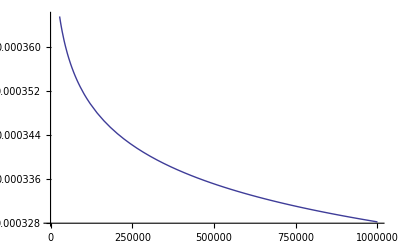

```mathematica
Plot[individden[x]*4.7*10^(-2)*x^(3/4),{x,10^(-2),10^6}]
```

```mathematica
80/1000/1000.
```

0.00008

```mathematica
{ConsumerGrowth,Starvation,Mortality,Recovery,StarveMaintenance,FullMaintenance,ResourceGrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
```

```mathematica
SteadyStateSol = FullSimplify[Solve[{
0 ==λ*F-σ*(1-R)*F +ρ* R * H,
0==σ*(1-R)*F - ρ* R*H - μ*H,
0 ==α*R*(1-R) -ρ*H*R -δ*H- β*F },{F,H,R}]
];
FSS = F/.SteadyStateSol[[3]]
HSS = H/.SteadyStateSol[[3]]
RSS = R/.SteadyStateSol[[3]]
```

-(α λ μ^2 (μ+ρ) (λ-σ))/((λ ρ+μ σ) (λ (δ λ+(β-λ) μ) ρ+μ (β μ+λ (δ+ρ)) σ))

-(α λ^2 μ (μ+ρ) (λ-σ))/((λ ρ+μ σ) (λ (δ λ+(β-λ) μ) ρ+μ (β μ+λ (δ+ρ)) σ))

(μ (-λ+σ))/(λ ρ+μ σ)

```mathematica
FullMaintenance/.M->1
```

1710.8

```mathematica
StarveMaintenance/.M->1
```

1710.8

```mathematica
Recovery/.M->1
```

2.52502×10^-6

```mathematica
Starvation/.M->1
```

0.000329022

```mathematica
ResourceGrowth/.M->1
```

2.1×10^-9